```mathematica
(*Código utilizado para obtener las secciones de Poincaré del sistema dada una energía y un k. Basado en el código fuente de Mathematica https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/poincare-sections.html. Adaptado al problema por Gustavo Ardila y Cristian Tibambre*)
(* lo hacemos con k=5.0*)
(*Constantes y parametro de control*)
k0=5;
m=5;
g=9.8;
```

```mathematica
(*Ecuaciones diferenciales*)
ecuaciones={p'[s]==-k0*(Sin[h[s]]-Sin[j[s]])*Cos[h[s]]-m*g*Sin[h[s]], h'[s]==p[s]/m, q'[s]==k0*(Sin[h[s]]-Sin[j[s]])*Cos[j[s]]-m*g*Sin[j[s]], j'[s]==q[s]/m};
```

```mathematica
(*Guarda la sección dada la solucion obtenida usando NDSolve y si esta cumple ciertas condiciones.*)
```

```mathematica
secciones[{a0_,b0_,c0_,d0_}]:=Reap[NDSolve[{ecuaciones, h[0]==a0, j[0]==b0, p[0]==c0, q[0]==d0, WhenEvent[q[s]==0, Sow[{h[s],p[s]}]]},{h[s],j[s], p[s], q[s]},{s,0,1000}, MaxSteps->Infinity]][[-1,1]];
```

```mathematica
(*Calcula la sección*)
info= Map[secciones, bunch]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{0.923846,-7.90858},{-0.167177,16.1821},{-0.707805,-12.7182},725,{-0.786255,-11.6837},{1.13656,0.683376},{-0.857718,10.5668}},253,{{1},838,{1}}}
 |  |  |  |

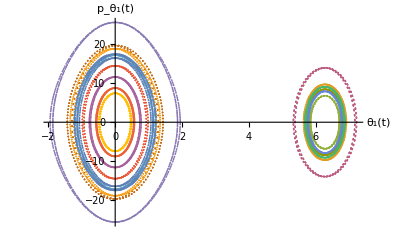

```mathematica
ListPlot[{info[[1]],info[[2]],info[[3]],info[[6]],info[[7]],info[[8]],info[[9]],info[[10]],info[[11]],info[[14]],info[[15]],info[[17]],info[[20]],info[[21]],info[[22]],info[[23]]}, ImageSize->Full, AxesLabel->{Style["θ_1(t)", Bold,20,Black], Style["p_θ_1(t)", Bold,20,Black]}]
```

```mathematica
8
```

```mathematica
Length[info]
```

260